```mathematica
G = CyclicGroup[6]
```

CyclicGroup[6]

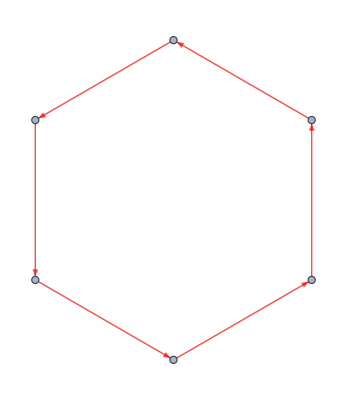

```mathematica
CayleyGraph[G]
```

```mathematica
AbelianGroup[6]
```

AbelianGroup[6]

```mathematica
AbelianGroup[{1,2}]
```

AbelianGroup[{1,2}]

```mathematica
CayleyGraph[AbelianGroup[{1,2}]]
```

-Graphics-

```mathematica
CayleyGraph[AbelianGroup[{1,2,3,4,5,6}]]
```

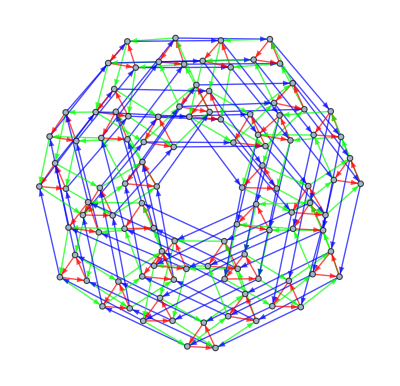

```mathematica
CayleyGraph[AbelianGroup[{1,3,5,7}]]
```

```mathematica
Solve[(3+3+2)==3^a]
```

{{a→ConditionalExpression[(2 ⅈ π C[1])/Log[3]+Log[8]/Log[3],C[1]∈Integers]}}

```mathematica
Solve[(a+a+a-1)==3^a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→(Log[3]-3 ProductLog[-Log[3]/3^(2/3)])/(3 Log[3])}}

```mathematica
Solve[(a+a+a-1)==3^n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→1/3 (1+3^n)}}

```mathematica
Solve[(a+a+a-2)==3^n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→1/3 (2+3^n)}}

```mathematica
Solve[1+2+3 == 3^n]
```

```mathematica
Solve[1+2+3 -n== 3^n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→(6 Log[3]-ProductLog[729 Log[3]])/Log[3]}}

```mathematica
(2n Log[n-1]-ProductLog[(n-1)^(2(n-1)) Log[n-1]])/Log[n-1]
```

(2 n Log[-1+n]-ProductLog[(-1+n)^(2 (-1+n)) Log[-1+n]])/Log[-1+n]

```mathematica
Plot[(2n Log[n-1]-ProductLog[(n-1)^(2(n-1)) Log[n-1]])/Log[n-1]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

```mathematica
PlotRange[(2 n Log[n-1]-ProductLog[(n-1)^(2 (n-1)) Log[n-1]])/Log[n-1],{n,0,20}]
```

```mathematica
(2 n Log[-1+n]-ProductLog[(-1+n)^(2 (-1+n)) Log[-1+n]])/Log[-1+n]
```

```mathematica
(2 n Log[-1+n]-ProductLog[(-1+n)^(2 (-1+n)) Log[-1+n]])/Log[-1+n]
```

(2 n Log[-1+n]-ProductLog[(-1+n)^(2 (-1+n)) Log[-1+n]])/Log[-1+n]

```mathematica
Plot[(2 n Log[-1+n]-ProductLog[(-1+n)^(2 (-1+n)) Log[-1+n]])/Log[-1+n],{n,0,100}]
```

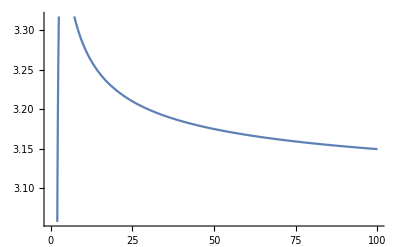

```mathematica
Solve[1+1/2+1/3 -1/n== 3^(1/n)]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→(6 Log[3])/(11 Log[3]-6 ProductLog[3 3^(5/6) Log[3]])}}

```mathematica
f[a_][x_]:=x^2+a;
eventualOrbit[a_]:=Drop[NestList[f[a],0.0,500],100];
column[a_]:={a,#}&/@eventualOrbit[a];
bifPic=Graphics[{PointSize[0.001],Opacity[0.1],Point[Flatten[Table[column[a],{a,-2,0,0.001}],1]]},AspectRatio->1/2]
```

```mathematica
f[n_] := (2n Log[n])/((2n^2-1) Log[n]-(2n) ProductLog[n n^((2n-1)/(2n)) Log[n]])
```

```mathematica
d[n_] := (2n^2-1);
```

```mathematica
f[3]
```

(6 Log[3])/(17 Log[3]-6 ProductLog[3 3^(5/6) Log[3]])

```mathematica
f[4]
```

(8 Log[4])/(31 Log[4]-8 ProductLog[8 2^(3/4) Log[4]])

```mathematica
f[5]
```

(10 Log[5])/(49 Log[5]-10 ProductLog[5 5^(9/10) Log[5]])

```mathematica
f[6]
```

(12 Log[6])/(71 Log[6]-12 ProductLog[6 6^(11/12) Log[6]])

```mathematica
f[7]
```

(14 Log[7])/(97 Log[7]-14 ProductLog[7 7^(13/14) Log[7]])

```mathematica
f[8]
```

(16 Log[8])/(127 Log[8]-16 ProductLog[32 2^(13/16) Log[8]])

```mathematica
f[9]
```

(18 Log[9])/(161 Log[9]-18 ProductLog[27 3^(8/9) Log[9]])

```mathematica
f[9.1]
```

0.136216

```mathematica
f[9+1/2]
```

(19 Log[19/2])/(359/2 Log[19/2]-19 ProductLog[19/2 (19/2)^(18/19) Log[19/2]])

```mathematica
f[5+1/2]
```

(11 Log[11/2])/(119/2 Log[11/2]-11 ProductLog[11/2 (11/2)^(10/11) Log[11/2]])

```mathematica
f[5/2]
```

(5 Log[5/2])/(23/2 Log[5/2]-5 ProductLog[5/2 (5/2)^(4/5) Log[5/2]])

```mathematica
f[3/2]
```

(3 Log[3/2])/(7/2 Log[3/2]-3 ProductLog[3/2 (3/2)^(2/3) Log[3/2]])

```mathematica
f[1+1/2]
```

(3 Log[3/2])/(7/2 Log[3/2]-3 ProductLog[3/2 (3/2)^(2/3) Log[3/2]])

```mathematica
f[1+1/3]
```

```mathematica
f[2+1/2]
```

(5 Log[5/2])/(23/2 Log[5/2]-5 ProductLog[5/2 (5/2)^(4/5) Log[5/2]])

```mathematica
f[3]
```

(6 Log[3])/(17 Log[3]-6 ProductLog[3 3^(5/6) Log[3]])

```mathematica
f[2]
```

(4 Log[2])/(7 Log[2]-4 ProductLog[2 2^(3/4) Log[2]])

```mathematica
f[500]
```

```mathematica
f[501]
```

(1002 Log[501])/(502001 Log[501]-1002 ProductLog[501 501^(1001/1002) Log[501]])

```mathematica
d[501]
```

502001

```mathematica
d[502]
```

504007

```mathematica
d[503]
```

506017

```mathematica
f[503]
```

(1006 Log[503])/(506017 Log[503]-1006 ProductLog[503 503^(1005/1006) Log[503]])

```mathematica
f[503+1/2]
```

(1007 Log[1007/2])/(1014047/2 Log[1007/2]-1007 ProductLog[1007/2 (1007/2)^(1006/1007) Log[1007/2]])

```mathematica
d[1014047 - 1007]
```

2052500083199

```mathematica
PrimeQ[d[26]]
```

False

```mathematica
f[26]
```

(52 Log[26])/(1351 Log[26]-52 ProductLog[26 26^(51/52) Log[26]])

```mathematica
FactorInteger[1351]
```

{{7,1},{193,1}}

```mathematica
f[999]
```

(1998 Log[999])/(1996001 Log[999]-1998 ProductLog[8991 3^(665/666) 37^(1997/1998) Log[999]])

```mathematica
PrimeQ[1996001]
```

False

```mathematica
FactorInteger[d[999]]
```

{{7,1},{313,1},{911,1}}

```mathematica
FactorInteger[d[9999]]
```

{{17,1},{191,1},{61583,1}}

```mathematica
FactorInteger[d[31231312]]
```

{{1950789698482687,1}}

```mathematica
FactorInteger[d[9994123412342]]
```

{{113,1},{463,1},{45972043303,1},{83055074111,1}}

```mathematica
FactorInteger[d[99941234134241324]]
```

{{47,1},{71,1},{1453369,1},{4118957516282524040891167,1}}

```mathematica
FactorInteger[d[999312312341234233231]]
```

{{47,1},{3593,1},{5920279,1},{1997722786466569929444512875969,1}}

```mathematica
PrimeQ[1997722786466569929444512875969]
```

True

```mathematica
1997722786466569929444512875969 * 5920279 * 3593 * 47
```

```mathematica
PrimeQ[1997250195193568970407352964145497009398721+2]
```

```mathematica
PrimeQ[1997250195193568970407352964145497009398721+6]
```

```mathematica
d[1^10*99]
```

19601

```mathematica
FactorInteger[19601]
```

{{17,1},{1153,1}}

```mathematica
Max[First/@{{17,1},{1153,1}}]
```

1153

```mathematica
PrimePi[1153]
```

191

```mathematica
d[1^10*99]
```

19601

```mathematica
FactorInteger[19601]
```

{{17,1},{1153,1}}

```mathematica
1153/19601
```

```mathematica
1/17


FactorInteger[d[1^10*22]]
```

1/17

{{967,1}}

```mathematica
FactorInteger[d[1^10*23]]
```

{{7,1},{151,1}}

```mathematica
FactorInteger[d[1^10*99]]
```

{{17,1},{1153,1}}

```mathematica
FactorInteger[d[3123471]]
```

{{31,1},{629423941151,1}}

```mathematica
3123471/629423941151
```

3123471/629423941151

```mathematica
N[3123471/629423941151]
```

4.96243×10^-6

```mathematica
N[3123471/629423941151,20]
```

4.9624280167803044681×10^-6

```mathematica
N[3123471/629423941151,24]
```

4.9624280167803044680599×10^-6

```mathematica
N[3123471/629423941151,28]
```

4.962428016780304468059904994×10^-6

```mathematica
N[3123471/629423941151,32]
```

4.9624280167803044680599049938632×10^-6

```mathematica
N[3123471/629423941151,36]
```

4.96242801678030446805990499386319712×10^-6

```mathematica
4.96242801678030446805990499386319711967654124381144611114255604271251265`36.*^-6 * 3
```

0.0000148872840503409134041797149815895914

```mathematica
d[100000]*4.96242801678030446805990499386319711967654124381144611114255604271251265`36.*^-6
```

99248.5603306436613444177954092040374

```mathematica
PrimeQ[99241]
```

True

```mathematica
{FactorInteger[Round[d[1231]*4.962]],Round[d[1231]*4.962]}
```

{{{2,1},{17,1},{73,2},{83,1}},15038438}

```mathematica
f[2]
```

(4 Log[2])/(7 Log[2]-4 ProductLog[2 2^(3/4) Log[2]])

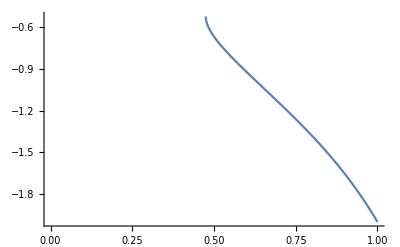

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
1+1
```

2



```mathematica
CayleyGraph[AbelianGroup[{1,1}]]
```

```mathematica
CayleyGraph[AbelianGroup[{2,2}]]
```

-Graphics-

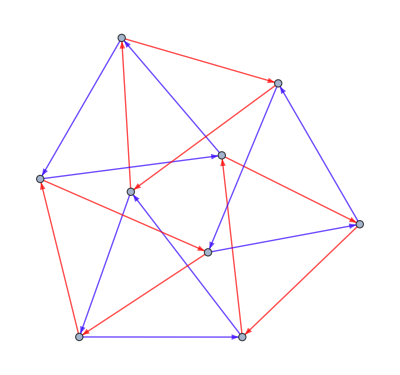

```mathematica
CayleyGraph[AbelianGroup[{3,3}]]
```

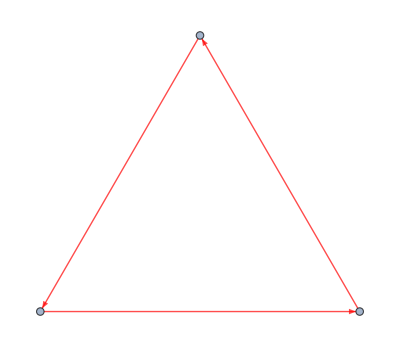

```mathematica
CayleyGraph[AbelianGroup[{3}]]
```

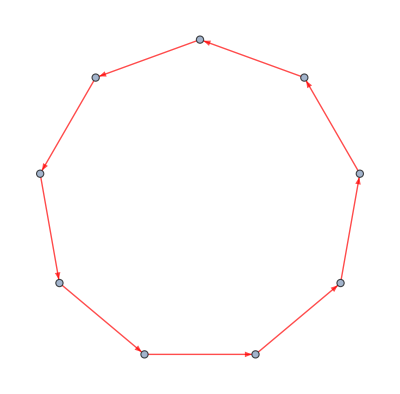

```mathematica
CayleyGraph[AbelianGroup[{9}]]
```

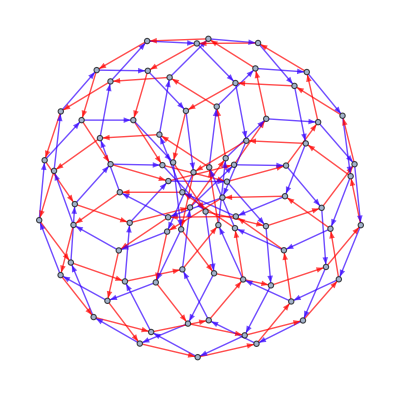

```mathematica
CayleyGraph[AbelianGroup[{9,9}]]
```

```mathematica
CayleyGraph[AbelianGroup[{2,9}]]
```

-Graphics-

```mathematica
CayleyGraph[AbelianGroup[{3,2}]]
```

-Graphics-

```mathematica
CayleyGraph[AbelianGroup[{3,9}]]
```

Set::write: Tag Inherited in Inherited["State"] is Protected.

```mathematica
d[n_] := (2n^2-1);
Do[
	Print[FactorInteger[
	{d[i]}]
	]
,{i,10}]
```